## AllPathCanyons

```mathematica
Table[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},i,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"],{i,1,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[{{"[◼]", "BranchialGraph"}}[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},i,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]],{i,1,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
shortestpaths=With[{vertices=VertexList[g]},Table[FindShortestPath[g,First[VertexList[g]],vertices[[i]]],{i,1,Length[vertices]}]]
```

{{{1,1}},{{1,1},{0,1}},{{1,1},{0,1},{1,1,0}},{{1,1},{0,1},{1,1,0},{0,0,1}},{{1,1},{0,1},{1,1,0},{1,0,1}},{{1,1},{0,1},{1,1,0},{0,0,1},{0,1,1,0}},{{1,1},{0,1},{1,1,0},{0,0,1},{1,1,0,1}},{{1,1},{0,1},{1,1,0},{1,0,1},{1,1,1,0}},{{1,1},{0,1},{1,1,0},{0,0,1},{0,1,1,0},{0,0,0,1}},{{1,1},{0,1},{1,1,0},{0,0,1},{0,1,1,0},{0,1,0,1}},{{1,1},{0,1},{1,1,0},{0,0,1},{0,1,1,0},{1,0,1,1,0}},{{1,1},{0,1},{1,1,0},{0,0,1},{1,1,0,1},{1,1,1,1,0}},{{1,1},{0,1},{1,1,0},{1,0,1},{1,1,1,0},{1,0,0,1}}}

```mathematica
Length[shortestpaths]
```

13

```mathematica
AllPathCanyons[g_]:=Table[ArrayPlot[Reverse@Transpose[PadRight[
With[{vertices=VertexList[g],randomInit=Table[RandomInteger[{0,1},3],8]},Table[FindShortestPath[g,First[VertexList[g]],vertices[[i]]],{i,1,Length[vertices]}]][[i]],{Automatic,Automatic},.25]],Frame->True,ColorRules->{0->Hue[.95,.4,1.4],1->Hue[.1,.1,.1]},Mesh->True],{i,1,Length[VertexList[g]]}]
```

```mathematica
AllPathCanyons[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,1},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},10,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]]
```

### Are certain paths within the mutliway tag system predictable? (E.g. )

### Do all paths belong to the same ‘class’ of ‘singleway’ tag system behavior (i.e. ‘explosive’, ‘degenerate’, and ‘periodic’)?

```mathematica
Table[Style[Text[Column[Row/@NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->Table[Prepend[RandomInteger[{0,1},4],s],10][[i]]}]&,IntegerDigits[18,2,5],30]]],FontFamily->"Roboto"],{i,1,10}]
```

{10010
101110
1100101
01010010
1001000
10001110
011101101
10110100
101000011
0000111000
011100000
10000000
000001101
00110100
1010000
00000100
0010000
000000
00000
0000
000
00
00
00
00
00
00
00
00
00
00,10010
100110
1100000
00001001
0100100
010000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
100001
0011111
111100
1001001
10010000
100000100
0001000010
100001000
0010000110
000011000
01100000
0000000
000000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
101110
1100101
01011111
1111100
11001001
010011101
01110100
1010000
00001111
0111100
110000
0001101
110100
1001101
11011010
110101110
1011100011
11000110110
001101100000
10110000000
100000001011
0000010111000
001011100000
01110000000
1000000000
00000000111
0000011100
001110000
11000000
000000101,10010
100010
0100011
001100
10000
000001
00100
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
101000
0000110
011000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
100000
0001011
101100
1001001
10011100
111000000
0000000101
000010100
01010000
1000000
00000000
0000000
000000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
101000
0001010
101000
0000100
010000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
100101
1010011
00111110
1111000
10000010
000100101
10010100
101000100
0001000110
100011000
0110001011
000101100
10110000
100000110
0001100011
110001100
0011000001
100000100
0001000010
100001000
0010001000
000100000
10000000
000001110
00111000
1100000
00000011
0001100
110000
0000111,10010
100001
0010011
001100
10000
001001
00100
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00}

```mathematica
Style[Text[Column[Row/@NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->Table[Prepend[RandomInteger[{0,1},4],s],10][[1]]}]&,IntegerDigits[18,2,5],30]]],FontFamily->"Roboto"]
```

## RandomPathCanyons

```mathematica
(* Visualize Multi-Way Systems and plot the Length of the strings for different particular paths, in the beginning will be randomized and then filtered. Take a multi-way graph, and the paths don't correspond to the same class of behavior. What kind of multi-way system has that? Correspondences between behavior classes and the multi-way system. Phase 2.

Phase 3. Finding correspondences between single-way & multi-way systems.  *)
```

```mathematica
AllPathCanyons[g_]:=Table[
ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True
],
{i,1,Length[VertexList[g]]}
]
```

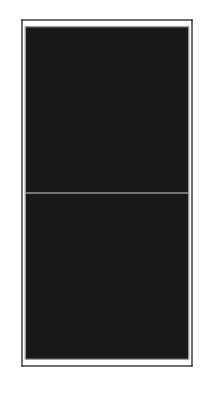
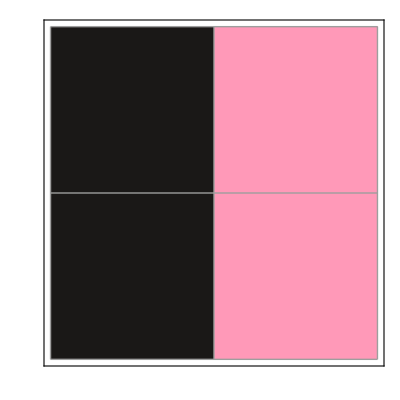
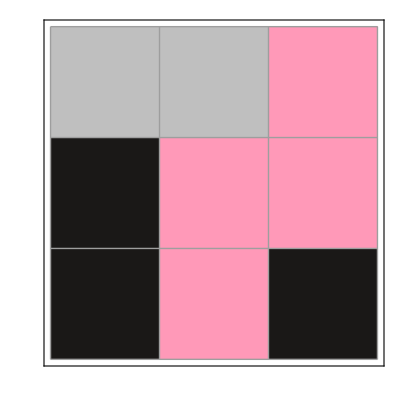
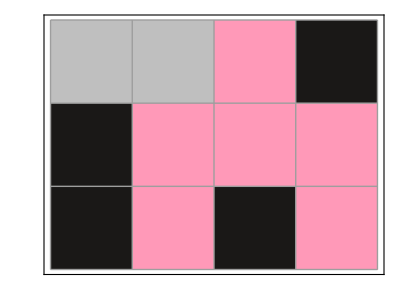
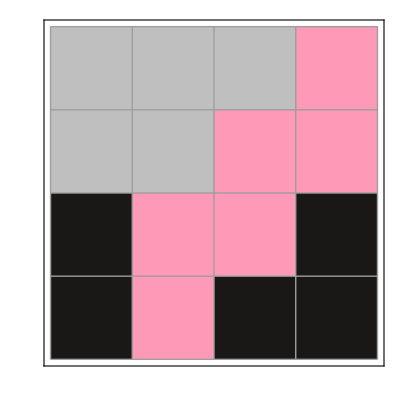
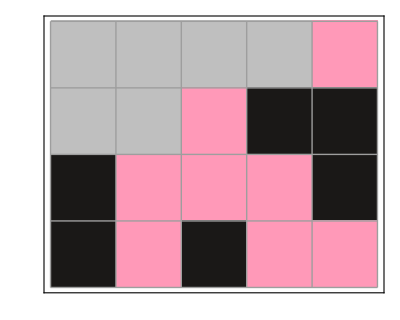
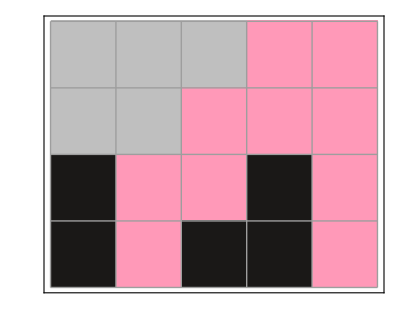
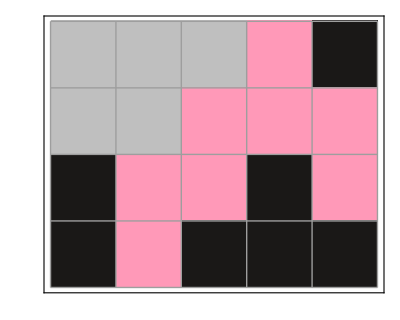
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}}

```mathematica
Table[
AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,1,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,0,1}],
{left___,0,1,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[i]]}]
}],
{{1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]],
{i,1,4}
]
```

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
Column[Row/@PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],Center]//. 0.25->"",
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
Table[
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,1,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,0,1}],
{left___,0,1,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[i]]}]
}],
{{1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]],
{i,1,4}
]
```

{{11
00,11
00
100,11
00
100
001,11
00
100
1100,11
00
100
001
0110,11
00
100
1100
0000,11
00
100
1100
1001,11
00
100
1100
11100,11
00
100
1100
0000
00100,11
00
100
001
0110
0101,11
00
100
001
0110
10110,11
00
100
1100
11100
10000,11
00
100
1100
11100
11001,11
00
100
1100
11100
111100},{11
01,11
01
110,11
01
110
001,11
01
110
101,11
01
110
001
0110,11
01
110
001
1100,11
01
110
101
1110,11
01
110
001
0110
0001,11
01
110
001
0110
0101,11
01
110
001
0110
10110,11
01
110
001
1100
1001,11
01
110
001
1100
11100,11
01
110
101
1110
1101},{11
10,11
10
01,11
10
01
110,11
10
01
110
010,11
10
01
110
101,11
10
01
110
010
001,11
10
01
110
010
0110,11
10
01
110
101
1110},{}}

Transpose[list]

```mathematica
Tuples[{0,1},2]
```

{{0,0},{0,1},{1,0},{1,1}}

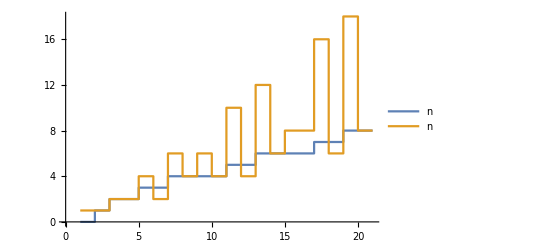

```mathematica
ListStepPlot[
{
Legended[
PrimePi[
Range[20]],
PrimePi[n]
],
Legended[
EulerPhi[Range[20]],
EulerPhi[n]
]
}
]
```

```mathematica
EulerPhi[Range[20]]
```

{1,1,2,2,4,2,6,4,6,4,10,4,12,6,8,8,16,6,18,8}

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
Table[
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,1,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,0,1}],
{left___,0,1,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[i]]}]
}],
{{1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]],
{i,1,4}
]
```

{{{{1,1},{0,0}},{{1,1,0.25},{0,0,0.25},{1,0,0}},{{1,1,0.25},{0,0,0.25},{1,0,0},{0,0,1}},{{1,1,0.25,0.25},{0,0,0.25,0.25},{1,0,0,0.25},{1,1,0,0}},{{1,1,0.25,0.25},{0,0,0.25,0.25},{1,0,0,0.25},{0,0,1,0.25},{0,1,1,0}},{{1,1,0.25,0.25},{0,0,0.25,0.25},{1,0,0,0.25},{1,1,0,0},{0,0,0,0}},{{1,1,0.25,0.25},{0,0,0.25,0.25},{1,0,0,0.25},{1,1,0,0},{1,0,0,1}},{{1,1,0.25,0.25,0.25},{0,0,0.25,0.25,0.25},{1,0,0,0.25,0.25},{1,1,0,0,0.25},{1,1,1,0,0}},{{1,1,0.25,0.25,0.25},{0,0,0.25,0.25,0.25},{1,0,0,0.25,0.25},{1,1,0,0,0.25},{0,0,0,0,0.25},{0,0,1,0,0}},{{1,1,0.25,0.25},{0,0,0.25,0.25},{1,0,0,0.25},{0,0,1,0.25},{0,1,1,0},{0,1,0,1}},{{1,1,0.25,0.25,0.25},{0,0,0.25,0.25,0.25},{1,0,0,0.25,0.25},{0,0,1,0.25,0.25},{0,1,1,0,0.25},{1,0,1,1,0}},{{1,1,0.25,0.25,0.25},{0,0,0.25,0.25,0.25},{1,0,0,0.25,0.25},{1,1,0,0,0.25},{1,1,1,0,0},{1,0,0,0,0}},{{1,1,0.25,0.25,0.25},{0,0,0.25,0.25,0.25},{1,0,0,0.25,0.25},{1,1,0,0,0.25},{1,1,1,0,0},{1,1,0,0,1}},{{1,1,0.25,0.25,0.25,0.25},{0,0,0.25,0.25,0.25,0.25},{1,0,0,0.25,0.25,0.25},{1,1,0,0,0.25,0.25},{1,1,1,0,0,0.25},{1,1,1,1,0,0}}},{{{1,1},{0,1}},{{1,1,0.25},{0,1,0.25},{1,1,0}},{{1,1,0.25},{0,1,0.25},{1,1,0},{0,0,1}},{{1,1,0.25},{0,1,0.25},{1,1,0},{1,0,1}},{{1,1,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{0,0,1,0.25},{0,1,1,0}},{{1,1,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{0,0,1,0.25},{1,1,0,0}},{{1,1,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{1,0,1,0.25},{1,1,1,0}},{{1,1,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{0,0,1,0.25},{0,1,1,0},{0,0,0,1}},{{1,1,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{0,0,1,0.25},{0,1,1,0},{0,1,0,1}},{{1,1,0.25,0.25,0.25},{0,1,0.25,0.25,0.25},{1,1,0,0.25,0.25},{0,0,1,0.25,0.25},{0,1,1,0,0.25},{1,0,1,1,0}},{{1,1,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{0,0,1,0.25},{1,1,0,0},{1,0,0,1}},{{1,1,0.25,0.25,0.25},{0,1,0.25,0.25,0.25},{1,1,0,0.25,0.25},{0,0,1,0.25,0.25},{1,1,0,0,0.25},{1,1,1,0,0}},{{1,1,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{1,0,1,0.25},{1,1,1,0},{1,1,0,1}}},{{{1,1},{1,0}},{{1,1},{1,0},{0,1}},{{1,1,0.25},{1,0,0.25},{0,1,0.25},{1,1,0}},{{1,1,0.25},{1,0,0.25},{0,1,0.25},{1,1,0},{0,1,0}},{{1,1,0.25},{1,0,0.25},{0,1,0.25},{1,1,0},{1,0,1}},{{1,1,0.25},{1,0,0.25},{0,1,0.25},{1,1,0},{0,1,0},{0,0,1}},{{1,1,0.25,0.25},{1,0,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{0,1,0,0.25},{0,1,1,0}},{{1,1,0.25,0.25},{1,0,0.25,0.25},{0,1,0.25,0.25},{1,1,0,0.25},{1,0,1,0.25},{1,1,1,0}}},{}}